# geo

```mathematica
a1={Sqrt[3]/2,-1/2};a2={Sqrt[3]/2,1/2};
b6={2*Pi/Sqrt[3],-2*Pi};b2={2*Pi/Sqrt[3],2*Pi};
Simplify[a1.b6];
Simplify[a2.b6];
Simplify[a1.b2];
Simplify[a2.b2];
kG={0,0}.{b6,b2};
kM={0,1/2}.{b6,b2};
kK={1/3,2/3}.{b6,b2};
```

```mathematica
kM
```

{π/(√3),π}

```mathematica
kK//Norm
```

(4 π)/3

```mathematica
a1//Norm
```

1

```mathematica
a1.b3
```

{(√3)/2,-1/2}.b3

```mathematica
a1.b2
```

0

```mathematica
a2.b
```

{(√3)/2,1/2}.b

```mathematica
b1=b6+b2;b4=-b1;b3=-b6;b5=-b2;
```

```mathematica
b={b1,b2,b3,b4,b5,b6};
```

```mathematica
gg2[ θ_]:=(θ 4π)/(√3){(√3)/2,-1/2};gg3[ θ_]:=(θ 4π)/(√3){(√3)/2,1/2};gg1 [ θ_]=gg2[ θ]-gg3[ θ];gg4[ θ_]:=-gg1[ θ];gg5[ θ_]=-gg2[ θ];gg6[ θ_]=-gg3[ θ];
```

```mathematica
bb={b2+b3,b3+b4,b4+b5,b5+b6,b6+b1,b1+b2}
```

{{0,4 π},{-2 √3 π,2 π},{-2 √3 π,-2 π},{0,-4 π},{2 √3 π,-2 π},{2 √3 π,2 π}}

```mathematica
{gg1[1],gg2[1],gg3[1],gg4[1],gg5[1],gg6[1]}
```

{{0,-(4 π)/(√3)},{2 π,-(2 π)/(√3)},{2 π,(2 π)/(√3)},{0,(4 π)/(√3)},{-2 π,(2 π)/(√3)},{-2 π,-(2 π)/(√3)}}

```mathematica
TA=5Pi/180;
```

```mathematica
gg2[TA]//Norm
```

π^2/(9 √3)

```mathematica
mkK= {TA 4 π/3, 0};mkM=TA{π,-π/(√3)};mkG={0,0};
```

# p6mm potential

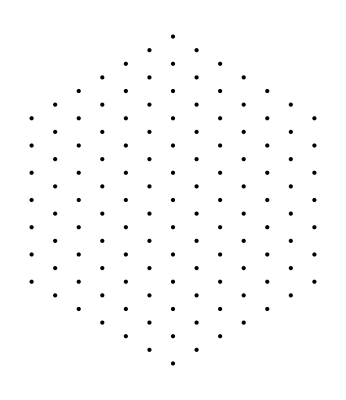

{Null^3}

```mathematica
n=6;Glength=Join[Table[i,{i,n+1,2n}],{2n+1},Table[i,{i,2n,n+1,-1}]];Gbegin=Table[Total@Glength[[1;;i]]-Glength[[i]]+1,{i,1,Length[Glength]}];G[θ_]:=Join[ArrayFlatten[Table[(n-i)gg5[ θ]+j gg1[ θ],{i,0,n},{j,-i,n}],1],ArrayFlatten[Table[(-i)gg5[ θ]+j gg1[ θ],{i,1,n},{j,-n,n-i}],1]];Graphics[Point[G[1]]]
{off1=ConstantArray[0,{Total@Glength,Total@Glength}];Table[off1[[i,i+1]]=1;,{j,1,2n+1},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-2}];}{off2=ConstantArray[0,{Total@Glength,Total@Glength}];
Table[off2[[i,i+Glength[[j]]+1]]=1;,{j,1,n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-1}];
Table[off2[[i,i+Glength[[j]]]]=1;,{j,n+1,2n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-2}];}{off3=ConstantArray[0,{Total@Glength,Total@Glength}];
Table[off3[[i,i+Glength[[j]]]]=1;,{j,1,n},{i,Gbegin[[j]],Gbegin[[j]]+Glength[[j]]-1}];
Table[off3[[i,i+Glength[[j]]-1]]=1;,{j,n+1,2n},{i,Gbegin[[j]]+1,Gbegin[[j]]+Glength[[j]]-1}];}
```

```mathematica
Glength//Total
```

127

```mathematica
GG1=G[1];
```

```mathematica
Gtest=G[1];
```

```mathematica
testoff[{a_,b_}]:=Graphics[{Arrowheads[0.01],Arrow[{Gtest[[a]],Gtest[[b]]}]}]
```

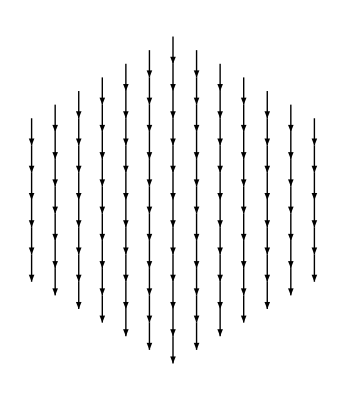

```mathematica
Show[Map[testoff,Position[off1,1]]]
```

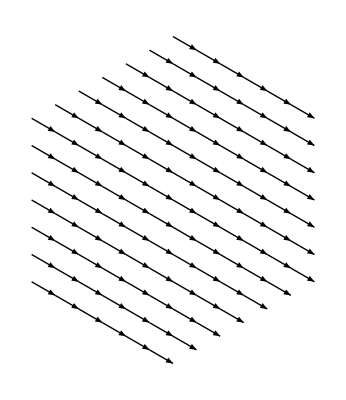

```mathematica
Show[Map[testoff,Position[off2,1]]]
```

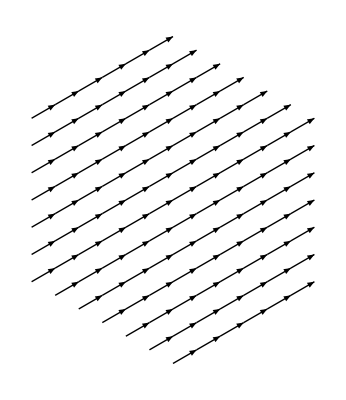

```mathematica
Show[Map[testoff,Position[off3,1]]]
```

```mathematica
off21[i_,j_]:=If[Norm[GG1[[j]]-GG1[[i]]-(gg1[ 1]+gg2[ 1])]<=0.01,1,0];off22[i_,j_]:=If[Norm[GG1[[j]]-GG1[[i]]-RotationMatrix[2Pi/3 ].(gg1[ 1]+gg2[ 1])]<=0.01,1,0];off23[i_,j_]:=If[Norm[GG1[[j]]-GG1[[i]]-RotationMatrix[4Pi/3].(gg1[ 1]+gg2[ 1])]<=0.01,1,0];
```

```mathematica
OFF21=Table[off21[i,j],{i,1,Glength//Total},{j,1,Glength//Total}];
OFF22=Table[off22[i,j],{i,1,Glength//Total},{j,1,Glength//Total}];OFF23=Table[off23[i,j],{i,1,Glength//Total},{j,1,Glength//Total}];
```

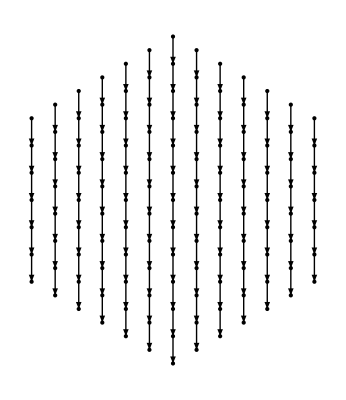

```mathematica
Show[Map[testoff,Position[off1,1]],Graphics[Point[G[1]]]]
```

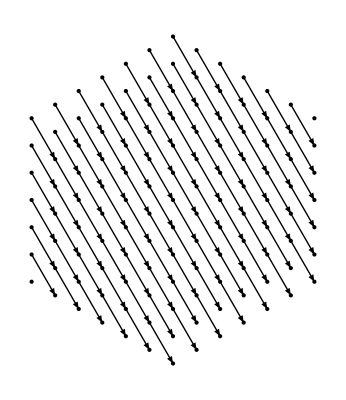

```mathematica
Show[Map[testoff,Position[OFF21,1]],Graphics[Point[G[1]]]]
```

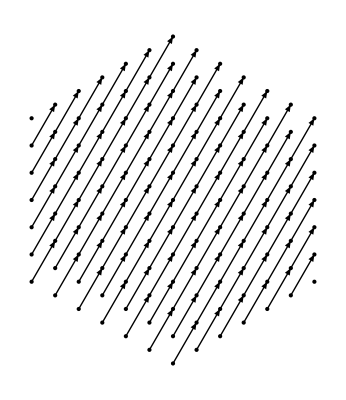

```mathematica
Show[Map[testoff,Position[OFF22,1]],Graphics[Point[G[1]]]]
```

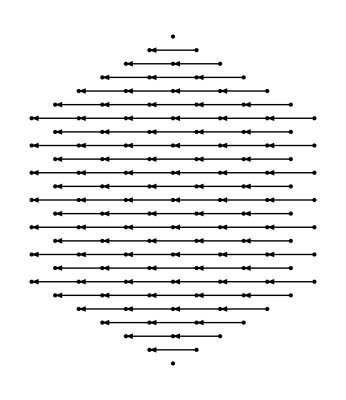

```mathematica
Show[Map[testoff,Position[OFF23,1]],Graphics[Point[G[1]]]]
```

# moire Hamiltonian

```mathematica
(kx+ⅈ ky)^3//Expand
```

kx^3+3 ⅈ kx^2 ky-3 kx ky^2-ⅈ ky^3

```mathematica
HcubicRashba[{kx_,ky_}]:={{10000-2(kx^2+ky^2)-6.1 (kx^2+ky^2)^2,ⅈ  5 (kx^3-3 ⅈ kx^2 ky-3 kx ky^2+ⅈ ky^3)},{-ⅈ  5 (kx^3+3 ⅈ kx^2 ky-3 kx ky^2-ⅈ ky^3),10000-2(kx^2+ky^2)-6.1 (kx^2+ky^2)^2}}
```

```mathematica
C6Rashba={{-ⅈ,0},{0,ⅈ}}
```

{{-ⅈ,0},{0,ⅈ}}

```mathematica
C6Rashba.HcubicRashba[{kx,ky}].Inverse[C6Rashba]-HcubicRashba[RotationMatrix[2Pi/6].{kx,ky}]//FullSimplify//Chop//FullSimplify//Chop
```

{{0,0},{0,0}}

```mathematica
MyRashba={{0,1},{-1,0}}
```

{{0,1},{-1,0}}

```mathematica
MyRashba.HcubicRashba[{kx,ky}].Inverse[MyRashba]-HcubicRashba[{kx,-ky}]//FullSimplify//Chop//FullSimplify
```

{{0,0},{0,0}}

```mathematica
HIntHcubRashba=Normal@BlockDiagonalMatrix@ParallelTable[ HcubicRashba[{kx,ky}+G[TA][[i]]],{i,1,Total@Glength}];diagHcubRashba[{kxx_,kyy_}]:=N@Chop@HIntHcubRashba/.{kx->kxx,ky->kyy};
```

```mathematica
Hinterationnrashba[V_]:=DiagonalMatrix[{V,V}];diaHrashba[V_]:=Chop@N@KroneckerProduct[off1+off2+off3+Transpose@off1+Transpose@off2+Transpose@off3,Hinterationnrashba[V]]
```

```mathematica
diaHrashba2[V2_]:=Chop@N@KroneckerProduct[OFF21+OFF22+OFF23+Transpose@OFF21+Transpose@OFF22+Transpose@OFF23,Hinterationnrashba[V2]]
```

```mathematica
TotalHam3cubRashba[{kx_,ky_},V_,V2_]:=Chop[N[diagHcubRashba[{kx,ky}]+diaHrashba2[V2]+diaHrashba[V]]];
```

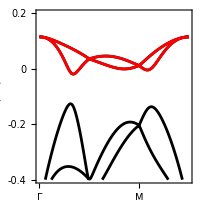

```mathematica
temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3cubRashba[k,-0.15,0]], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p0=ListLinePlot[temp-10000, PlotRange ->{-0.4,0.2}, Frame -> True, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{{-0.4,-0.2,0,0.2},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,20],FrameLabel->{"","E (eV)"},FrameStyle->Directive[20,Black],LabelStyle->Directive[20,Black],ImageSize->200];p1=ListLinePlot[temp[[{-2,-1}]]-10000, PlotRange ->{-0.4,0.2}, Frame -> True, AspectRatio -> 1,PlotStyle->Red,FrameTicks->{{{-0.4,-0.2,0,0.2},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,20],FrameLabel->{"","E (eV)"},FrameStyle->Directive[20,Black],LabelStyle->Directive[20,Black],ImageSize->200];Show[p0,p1]
```

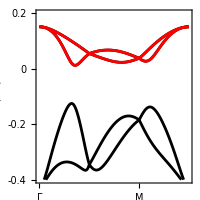

```mathematica
temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3cubRashba[k,-0.15,0.08]], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p0=ListLinePlot[temp-10000, PlotRange ->{-0.4,0.2}, Frame -> True, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{{-0.4,-0.2,0,0.2},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,16],FrameLabel->{"","E (eV)"},FrameStyle->Directive[16,Black],LabelStyle->Directive[16,Black],ImageSize->200];p1=ListLinePlot[temp[[{-2,-1}]]-10000, PlotRange ->{-0.4,0.2}, Frame -> True, AspectRatio -> 1,PlotStyle->Red,FrameTicks->{{{-0.4,-0.2,0,0.2},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,16],FrameLabel->{"","E (eV)"},FrameStyle->Directive[16,Black],LabelStyle->Directive[16,Black],ImageSize->200];Show[p0,p1]
```

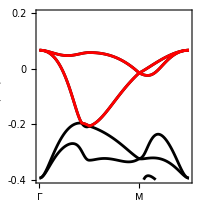

```mathematica
temp=Transpose@ParallelTable[Sort@Eigenvalues[TotalHam3cubRashba[k,0.08,0.08]], {k, Join[Table[λ mkK, {λ, 0, 1, 0.01}], Table[mkK+ λ (mkM- mkK), {λ, 0.01, 1, 0.01}], Table[mkM+ λ (mkG-mkM), {λ, 0.01, 1, 0.01}]]}];p0=ListLinePlot[temp-10000, PlotRange ->{-0.4,0.2}, Frame -> True, AspectRatio -> 1,PlotStyle->Black,FrameTicks->{{{-0.4,-0.2,0,0.2},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,16],FrameLabel->{"","E (eV)"},FrameStyle->Directive[16,Black],LabelStyle->Directive[16,Black],ImageSize->200];p1=ListLinePlot[temp[[{-2,-1}]]-10000, PlotRange ->{-0.4,0.2}, Frame -> True, AspectRatio -> 1,PlotStyle->Red,FrameTicks->{{{-0.4,-0.2,0,0.2},None},{{{1,"Γ"},{101,"K"},{201,"M"},{301,"Γ"}},None}},FrameTicksStyle->Directive[Black,16],FrameLabel->{"","E (eV)"},FrameStyle->Directive[16,Black],LabelStyle->Directive[16,Black],ImageSize->200];Show[p0,p1]
```

# phase

```mathematica
num=40;BZ=Flatten[Table[j mkK+i RotationMatrix[2Pi/6].mkK,{i,0,0.5,1/num},{j,i,1-i,1/num}],1];
```

```mathematica
BZ//Dimensions
```

{441,2}

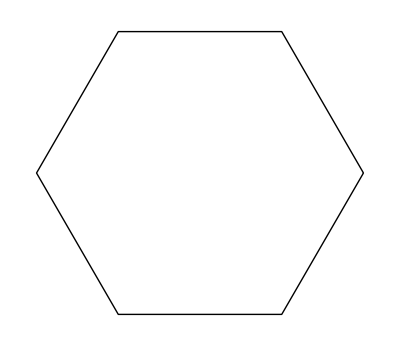

```mathematica
unitcell=Graphics@Line@Table[RotationMatrix[2Pi/6 J].mkK,{J,0,6}]
```

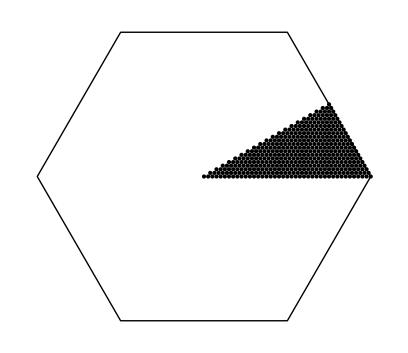

```mathematica
Show[Graphics@Point@BZ,unitcell]
```

```mathematica
Dispersionall[{v_,v2_}]:=ParallelTable[Sort@Eigenvalues@TotalHam3cubRashba[k,v,v2],{k,BZ}];
```

```mathematica
getGap[{l_,v_}]:=With[{t=Dispersionall[{l,v}]},t[[;;,-2]]-t[[;;,-3]]//Chop//Min]
```

```mathematica
getGap[{-0.01,0.1}]//AbsoluteTiming
```

{1.91759,0.016697}

```mathematica
Parameterspace1=Flatten[Table[{i,j},{i,0.1,-0.2,-0.2/30},{j,-0.1,0.1,0.2/30}],1];
```

```mathematica
Parameterspace1//Dimensions
```

{1426,2}

```mathematica
GapALL=Table[getGap[p],{p,Parameterspace1}];
```

```mathematica
GapALL
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0047114,0.0048263,0.00508323,0.00544393,0.0058719,0.00612344,0.00596793,0.00588935,0.00587994,0.00592969,0.0060276,0.00616287,0.00632585,0.00650867,0.0067055,0.00691271,0.00712885,0.00735456,0.00759253,0.00784733,0.0081252,0.00843381,0.00878184,0.00917853,0.00963301,0.00981814,0.00985912,0.00999389,0.0102496,0.0106501,0.0112133,0.00900536,0.009616,0.00986864,0.0101937,0.0105764,0.0110024,0.0114591,0.0119355,0.0121517,0.0123549,0.0126041,0.0128939,0.0132198,0.0135776,0.0139643,0.0143774,0.0148157,0.0152787,0.0157668,0.0162813,0.0168243,0.0173985,0.0180074,0.0186149,0.0190177,0.019453,0.0199305,0.0204603,0.0209524,0.0213589,0.0218454,0.0121038,0.0126461,0.0132376,0.0138669,0.0145242,0.0152009,0.0158901,0.0165857,0.0172829,0.0179776,0.0186668,0.019348,0.0199382,0.0204695,0.0210374,0.0216399,0.0222758,0.022944,0.0236443,0.024377,0.0250497,0.0256615,0.0262809,0.0269129,0.0275631,0.0282374,0.0289424,0.0296848,0.0304716,0.0313099,0.0322066,0.0161126,0.0166462,0.01724,0.0178854,0.0185745,0.0193001,0.0200558,0.0208361,0.0216361,0.022452,0.0232804,0.0241186,0.0249647,0.0258172,0.0266753,0.0275386,0.0284073,0.029282,0.0301638,0.0310543,0.0319554,0.0328695,0.0337995,0.0347485,0.0357199,0.0367174,0.0377451,0.0388071,0.0399078,0.0410515,0.0422427,0.0203009,0.0208848,0.0215339,0.0222417,0.0230016,0.0238078,0.0246548,0.0255376,0.026452,0.027394,0.0283606,0.029349,0.0303571,0.0313832,0.0324261,0.0334848,0.0345592,0.0356492,0.0367552,0.0378778,0.0390183,0.0401779,0.0413584,0.0425616,0.0437897,0.0450452,0.0463305,0.0476484,0.0490017,0.0503933,0.0518262,0.024255,0.0250933,0.0258239,0.0266176,0.027469,0.0283729,0.0293245,0.0303195,0.0313539,0.0324241,0.0335271,0.0346603,0.0358213,0.0370083,0.0382199,0.039455,0.0407128,0.0419928,0.043295,0.0446195,0.0459667,0.0473374,0.0487323,0.0501527,0.0515998,0.0530751,0.0545802,0.0561169,0.0576871,0.0592925,0.0609354,0.027588,0.0287375,0.0299284,0.0308918,0.0318446,0.0328545,0.033917,0.0350282,0.0361844,0.0373823,0.0386188,0.0398915,0.0411979,0.0425362,0.0439047,0.0453021,0.0467274,0.0481798,0.0496589,0.0511642,0.0526959,0.0542541,0.0558391,0.0574515,0.059092,0.0607613,0.0624606,0.0641908,0.065953,0.0677486,0.0695788,0.0309896,0.0322217,0.0335017,0.0348246,0.0360761,0.0371953,0.0383709,0.0395992,0.0408766,0.0422,0.0435664,0.0449734,0.0464186,0.0478999,0.0494156,0.0509643,0.0525447,0.0541559,0.0557969,0.0574673,0.0591667,0.0608948,0.0626516,0.0644371,0.0662518,0.0680958,0.0699697,0.0718741,0.0738095,0.0757767,0.0777764,0.0343793,0.0357008,0.037075,0.0384972,0.0399633,0.0413738,0.0426626,0.0440069,0.0454036,0.0468496,0.0483419,0.049878,0.0514556,0.0530727,0.0547273,0.0564179,0.0581431,0.0599017,0.0616926,0.0635152,0.0653686,0.0672524,0.0691663,0.0711099,0.0730833,0.0750863,0.0771191,0.0791819,0.0812748,0.0833982,0.0855525,0.0377135,0.0391285,0.0406,0.0421234,0.0436947,0.0453101,0.0467858,0.0482444,0.0497578,0.0513228,0.0529367,0.0545969,0.0563011,0.0580472,0.0598332,0.0616575,0.0635185,0.0654148,0.0673454,0.0693091,0.0713051,0.0733327,0.0753912,0.0774802,0.0795992,0.081748,0.0839264,0.0861341,0.0883713,0.0906377,0.0929335,0.0409699,0.0424808,0.044051,0.0456762,0.0473524,0.049076,0.0507434,0.0523138,0.0539407,0.0556211,0.0573523,0.0591317,0.060957,0.0628259,0.0647365,0.066687,0.0686758,0.0707013,0.0727624,0.0748577,0.0769863,0.0791472,0.0813397,0.0835629,0.0858163,0.0880994,0.0904117,0.0927394,0.0950424,0.0973793,0.0997495,0.0441382,0.0457461,0.0474155,0.0491422,0.0509224,0.0527525,0.0545424,0.0562218,0.0579591,0.0597512,0.0615955,0.0634893,0.0654303,0.0674163,0.0694452,0.0715152,0.0736245,0.0757716,0.077955,0.0801734,0.0824257,0.0847108,0.0870276,0.0893753,0.091651,0.0939578,0.0963005,0.098678,0.101089,0.103533,0.106009,0.0472155,0.0489207,0.050689,0.0525164,0.054399,0.0563335,0.0581922,0.0599778,0.0618221,0.0637223,0.0656755,0.0676792,0.0697309,0.0718286,0.0739699,0.0761531,0.0783763,0.0806379,0.0829364,0.0852702,0.0876382,0.0899835,0.0922814,0.0946182,0.0969926,0.0994032,0.101849,0.104328,0.10684,0.109384,0.111945,0.0502031,0.0520052,0.0538716,0.0557983,0.0577816,0.0598182,0.0617032,0.063592,0.0655401,0.0675446,0.0696028,0.071712,0.0738698,0.0760739,0.0783223,0.0806129,0.082944,0.0853137,0.0877204,0.0901107,0.0924267,0.0947842,0.0971815,0.0996171,0.102089,0.104597,0.107139,0.109713,0.112179,0.114667,0.117189,0.0531047,0.055003,0.0569663,0.0589907,0.0610727,0.0631596,0.0650861,0.0670752,0.0691238,0.0712291,0.0733883,0.0755988,0.0778581,0.080164,0.0825144,0.0849071,0.0873403,0.0898122,0.0921469,0.0945153,0.0969264,0.0993782,0.101869,0.104397,0.106962,0.109526,0.111985,0.114482,0.117014,0.119581,0.122181,0.0559255,0.0579188,0.0599775,0.0620979,0.0642764,0.0663276,0.0683514,0.0704378,0.0725838,0.0747864,0.0770429,0.0793507,0.0817073,0.0841104,0.0865579,0.0890477,0.0914968,0.0938665,0.0962819,0.098741,0.101242,0.103783,0.106362,0.108951,0.11141,0.11391,0.116447,0.119021,0.121629,0.12427,0.126943,0.0586714,0.0607583,0.0629109,0.0651252,0.0673379,0.0693908,0.0715093,0.0736901,0.0759302,0.0782268,0.080577,0.0829783,0.0854281,0.0879242,0.0904644,0.0928882,0.0952985,0.0977557,0.100258,0.102803,0.105389,0.108014,0.1105,0.112996,0.115532,0.118106,0.120717,0.123363,0.126042,0.128752,0.131493,0.0613487,0.0635277,0.0657722,0.0680784,0.0702134,0.0723588,0.0745693,0.0768417,0.079173,0.0815602,0.0840006,0.0864917,0.0890309,0.0916159,0.0940221,0.0964685,0.0989631,0.101504,0.104088,0.106715,0.109295,0.111781,0.114309,0.116878,0.119486,0.122131,0.124811,0.127525,0.13027,0.132839,0.135428,0.0639636,0.066233,0.0685675,0.0708375,0.0730051,0.0752406,0.0775405,0.0799016,0.082321,0.0847958,0.0873231,0.0899005,0.0924953,0.0949215,0.0973997,0.0999275,0.102503,0.105123,0.107786,0.110303,0.112816,0.115374,0.117973,0.120611,0.123287,0.125999,0.128744,0.131344,0.133924,0.136537,0.139182,0.0665221,0.0688801,0.0712796,0.0734653,0.0757214,0.0780444,0.0804311,0.0828783,0.0853829,0.0879421,0.0905531,0.0931538,0.0956066,0.0981129,0.10067,0.103276,0.105928,0.108598,0.11109,0.113629,0.116212,0.118838,0.121504,0.124208,0.126949,0.12962,0.132185,0.134786,0.137421,0.140089,0.142604,0.06903,0.0714746,0.0737548,0.0760276,0.0783699,0.0807781,0.083249,0.0857794,0.0883664,0.091007,0.0936198,0.0960958,0.0986267,0.10121,0.103843,0.106523,0.109161,0.111676,0.114237,0.116844,0.119494,0.122185,0.124915,0.127681,0.130239,0.132824,0.135445,0.138101,0.14073,0.143183,0.14567,0.0714926,0.0738877,0.0761736,0.0785314,0.0809575,0.0834485,0.0860011,0.0886121,0.0912787,0.0939095,0.0964055,0.0989579,0.101564,0.104221,0.106927,0.109544,0.112077,0.114659,0.117287,0.119958,0.122672,0.125425,0.128114,0.130677,0.133279,0.135918,0.138592,0.141123,0.143589,0.146089,0.148621,0.0738769,0.0761724,0.0785424,0.0809831,0.0834908,0.0860621,0.0886939,0.0913829,0.0940375,0.0965507,0.0991216,0.101748,0.104426,0.107154,0.109759,0.112309,0.114909,0.117556,0.120247,0.12298,0.125754,0.128369,0.130947,0.133566,0.136221,0.138912,0.14136,0.143838,0.14635,0.148894,0.15147,0.0760361,0.0784151,0.0808671,0.0833883,0.0859753,0.0886247,0.0913331,0.094017,0.0965446,0.0991314,0.101775,0.104472,0.10722,0.109822,0.112387,0.115002,0.117665,0.120373,0.123125,0.125918,0.128472,0.131064,0.133697,0.136367,0.139002,0.141454,0.143942,0.146465,0.14902,0.151605,0.15392,0.0781604,0.0806208,0.0831527,0.0857524,0.0884164,0.0911414,0.0938599,0.0963994,0.0989996,0.101658,0.104371,0.107136,0.109744,0.112321,0.11495,0.117627,0.120351,0.12312,0.125873,0.128435,0.13104,0.133685,0.136369,0.138954,0.141415,0.143912,0.146445,0.149011,0.151522,0.153843,0.156195,0.0802545,0.0827943,0.0854041,0.0880801,0.0908188,0.0935771,0.096126,0.0987373,0.101408,0.104135,0.106915,0.109536,0.112124,0.114764,0.117454,0.120192,0.122975,0.125698,0.128269,0.130885,0.133542,0.136238,0.138786,0.141254,0.14376,0.146302,0.148877,0.151328,0.153654,0.156012,0.158401,0.0823227,0.0849399,0.0876253,0.0903753,0.0931782,0.0957344,0.0983545,0.101035,0.103774,0.106568,0.109208,0.111805,0.114455,0.117157,0.119906,0.122702,0.125404,0.127985,0.13061,0.133277,0.135984,0.138506,0.140981,0.143494,0.146044,0.148627,0.151033,0.153363,0.155726,0.158121,0.160288,0.0843688,0.0870612,0.0898202,0.0926421,0.0952336,0.0978605,0.10055,0.103298,0.106103,0.10877,0.111374,0.114033,0.116743,0.119503,0.12231,0.125002,0.12759,0.130223,0.132899,0.135616,0.138122,0.140603,0.143123,0.14568,0.148271,0.150643,0.152977,0.155345,0.157744,0.159887,0.16201,0.0863959,0.0891616,0.0919919,0.0946319,0.0972636,0.0999591,0.102715,0.105529,0.10823,0.110839,0.113504,0.116223,0.118991,0.121808,0.124499,0.127093,0.129733,0.132417,0.135142,0.137643,0.140129,0.142655,0.145218,0.147816,0.150165,0.152503,0.154875,0.157278,0.159408,0.161532,0.163687,0.0884072,0.0912439,0.0939369,0.0965714,0.0992713,0.102033,0.104854,0.107595,0.110208,0.112878,0.115603,0.118379,0.121204,0.123903,0.126502,0.129148,0.131838,0.134571,0.137076,0.139566,0.142096,0.144664,0.147269,0.149606,0.151947,0.154322,0.15673,0.158857,0.160982,0.163138,0.165323}

```mathematica
data1=Map[Flatten,Transpose@{Parameterspace1,GapALL}];
```

```mathematica
p0=ListDensityPlot[data1,ColorFunction->(ColorData["SunsetColors"]@(Rescale[#,{0,0.17}])&),ColorFunctionScaling->False, ImageSize ->Large,PlotLegends->Automatic,InterpolationOrder->All,AspectRatio ->3/4,FrameTicksStyle->Directive[Black,15],LabelStyle->Directive[15,Black],PlotRange->{-0.1,0.16},ClippingStyle->Automatic];
```

```mathematica
p1=ListContourPlot[data1,Contours->{0},ContourShading->None,ContourStyle->{{Opacity[1],Red,Thickness[0.01/1.5],Dashed}}];
```

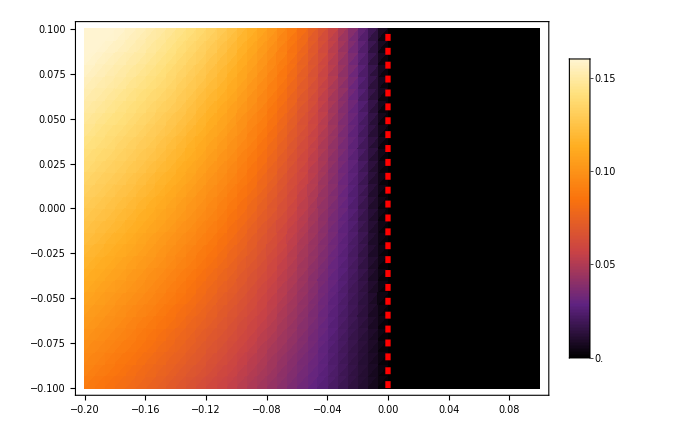

```mathematica
Show[p0,p1]
```

```mathematica
PPGMK2[{a_,b_},c_]:=Graphics[{Thickness[0.1/15],Blue,Opacity[1],Line[{{a,b}+c{1,1},{a,b}-c{1,1}}],Line[{{a,b}+c{-1,1},{a,b}-c{-1,1}}]}];PPGMK0[{a_,b_},c_]:=Graphics[{Thickness[0.1/15],Red,Opacity[1],Line[{{a,b}+c{1,1},{a,b}-c{1,1}}],Line[{{a,b}+c{-1,1},{a,b}-c{-1,1}}]}];
```

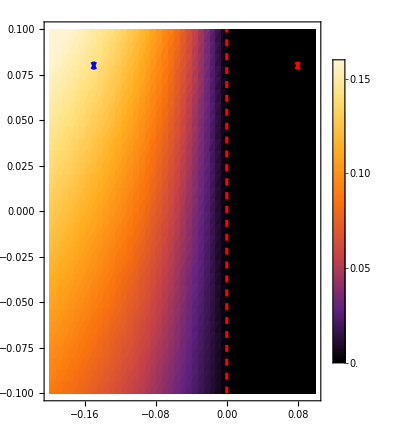

```mathematica
Show[p0,p1,PPGMK0[{0.08,0.08},0.002],PPGMK2[{-0.15,0.08},0.002],AspectRatio->1.3,FrameTicksStyle->{FontSize->20,FontWeight->"Bold",FontFamily->"Times"},BaseStyle->{FontSize->20,FontWeight->"Bold"},ImageSize->400]
```